# Mutation distribution fitting

```mathematica
(* Global configuration*)
export = True; (* True to export images *)
On[Assert];
```

## Data input

## Set working directory

```mathematica
SetDirectory[NotebookDirectory[]<>"results"]
```

/mnt/Ad115_PC/Programming_pc/Bioinformatica/ICGC/ICGC-data-parser/mutation-distribution-workflow/results

## Import data

```mathematica
data = Import["all.BRCA-EU.mutations-distribution.tsv"]; 
(* Tests *)
data[[;;2]]
data[[-10;;]]
```

{{# Project: BRCA-EU,Gene: All},{MUTATIONS_COUNT,GENE_COUNT,GENES}}

{{3051,1,ENSG00000172264,},{3291,1,ENSG00000188107,},{3328,1,ENSG00000150275,},{3350,1,ENSG00000066032,},{3570,1,ENSG00000185565,},{3644,1,ENSG00000153707,},{4009,1,ENSG00000198947,},{4059,1,ENSG00000078328,},{4063,1,ENSG00000183117,},{4847,1,ENSG00000174469,}}

## Lower distribution

I was advised to lower the distribution so that the minimum value was zero, in order to improve the quality of the predictions.
Whether or not this is true, this section does exactly that.

```mathematica
(* Decrease the Y value by 1*)
(*
loweredData = Join[
data[[;;2]], 
Map[({#[[1]], #[[2]]-1, #[[3]]})&, data[[3;;]]]
];
(* Some tests *)
loweredData[[;;2]]
loweredData[[-10;;]]
*)
```

## Structure data as a Dataset

```mathematica
(*Get cancer project*)
project = StringSplit[
StringSplit[data[[1,1]], ","][[1]],
":"
][[2]]

(*Get genes analized*)
gene = StringSplit[
StringSplit[data[[1,2]], ","][[1]],
":"
][[2]]

(*Get column headers*)
headers = data[[2]]
```

BRCA-EU

All

{MUTATIONS_COUNT,GENE_COUNT,GENES}

```mathematica
(*Converts a line from the imported data to an association apt for being added to a dataset*)
LineToDataset = Association[
Join[
Table[ <|headers[[i]]->#[[i]]|>, {i, 3}], {"PROJECT"->project, "GENE"->gene}
]
]&
(* Test the new function *)
line = data[[500]]
LineToDataset[line]
```

Association[Join[Table[Association[headers⟦i⟧→#1⟦i⟧],{i,3}],{PROJECT→project,GENE→gene}]]&

{510,3,ENSG00000182197,ENSG00000134775,ENSG00000136928,}

<|MUTATIONS_COUNT→510,GENE_COUNT→3,GENES→ENSG00000182197,ENSG00000134775,ENSG00000136928,PROJECT→ BRCA-EU,GENE→ All|>

```mathematica
(* Convert the imported data to a dataset *)
dataset = Dataset[ LineToDataset /@ data[[3;;]] ]
(*Some tests*)
dataset[500]
data[[502]]
dataset[Total,"GENE_COUNT"]
Total[ (#[[2]])& /@ data[[3;;]]]
```

Dataset[<>]

Dataset[<>]

{512,1,ENSG00000113391,}

39985

39985

## Get unformatted distribution

```mathematica
(* Get distribution from the dataset *)
distribution = Partition[
(* Make pairs of values, similar to a zipper*)
Riffle[
(* Take the X values *)
Normal[ dataset[All, "MUTATIONS_COUNT"] ],
(* Take the Y values *)
Normal[ dataset[All, "GENE_COUNT"] ]
], 2
];
(* Some tests *)
Assert[
distribution[[-1, All]] == data[[-1,;;2]] 
]
distribution[[;;10]]
```

{{1,968},{2,865},{3,901},{4,811},{5,823},{6,840},{7,893},{8,977},{9,1055},{10,1110}}

## Expand into sampled data

```mathematica
(* Expands a {v, r} pair into r repetitions of v *)
expandPair = Table[#[[1]], #[[2]]]&;
(* Test the new function *)
expandPair[{2, 3}]
Join@@(expandPair /@ {{1,2}, {3,4}, {4,5}})
```

{2,2,2}

{1,1,3,3,3,3,4,4,4,4,4}

```mathematica
(* Expand the distribution into the original samples *)
rawSamples = Join@@(expandPair/@ distribution)
(* Some tests *)
Dimensions[rawSamples]
dataset[Total, "GENE_COUNT"]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,39829,1450,1459,1463,1470,1475,1478,1480,1496,1497,1511,1511,1538,1544,1561,1563,1564,1575,1578,1582,1584,1595,1601,1604,1607,1610,1623,1634,1642,1660,1665,1691,1699,1742,1805,1807,1808,1820,1860,1874,1878,1879,1900,1922,1937,1948,1951,1965,1972,1973,2001,2002,2011,2024,2093,2110,2132,2179,2224,2276,2286,2462,2620,2640,2658,2780,2850,2868,2980,3051,3291,3328,3350,3570,3644,4009,4059,4063,4847}
 |  |  |  |

{39985}

39985

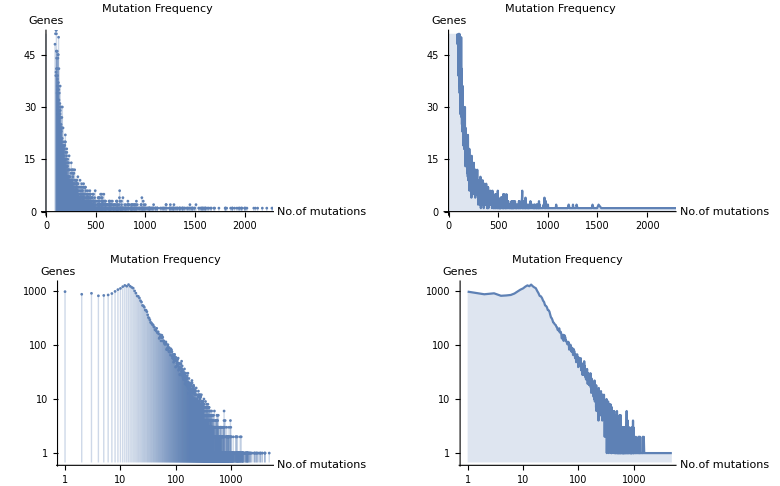

```mathematica
GraphicsGrid[
{
{
ListPlot[#, 
Filling->Bottom, ImageSize->Medium, PlotLabel->"Mutation Frequency", AxesLabel->{"No.of mutations","Genes"}
], 
ListPlot[#, 
Filling->Bottom, Joined -> True,ImageSize->Medium, PlotLabel->"Mutation Frequency", AxesLabel->{"No.of mutations","Genes"}
]
},
{
ListLogLogPlot[#, 
Filling->Bottom, ImageSize->Medium, PlotLabel->"Mutation Frequency", AxesLabel->{"No.of mutations","Genes"}
], 
ListLogLogPlot[#, 
Filling->Bottom, Joined -> True,ImageSize->Medium, PlotLabel->"Mutation Frequency", AxesLabel->{"No.of mutations","Genes"}
]
}
}
]& @ distribution
```

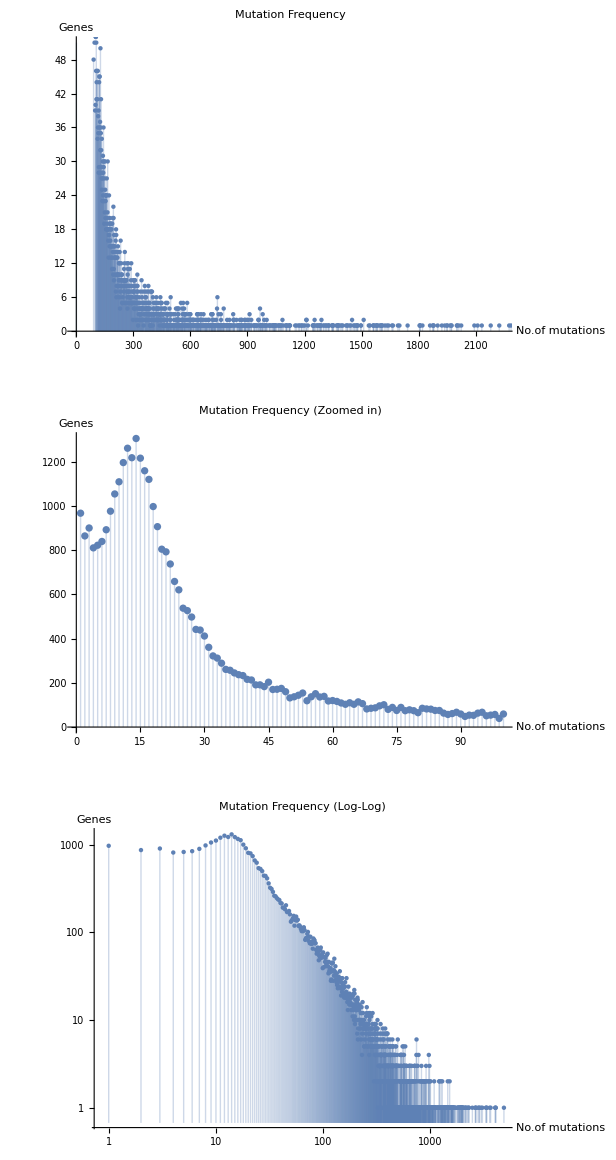

```mathematica
freqPlot=GraphicsGrid[
{{ListPlot[#, 
Filling->Bottom,ImageSize->Large, PlotLabel->"Mutation Frequency", AxesLabel->{"No.of mutations","Genes"}
]},
{
ListPlot[#[[;;100]], 
Filling->Bottom,ImageSize->Large, PlotLabel->"Mutation Frequency (Zoomed in)", AxesLabel->{"No.of mutations","Genes"}
]}, 
{ListLogLogPlot[#, 
Filling->Bottom, Joined -> False,ImageSize->Large, PlotLabel->"Mutation Frequency (Log-Log)", AxesLabel->{"No.of mutations","Genes"}
]
}}
]&[distribution]
```

```mathematica
If[ export,
Export["./freqPlot.png", freqPlot]
]
```

./freqPlot.png

## Main genes localization

We define an association with all the genes we may be interested in

```mathematica
(* Gene -> GeneID association *)
geneIDs = <|
"MDM2"-> "ENSG00000135679", "AKT1"-> "ENSG00000142208",
"CHEK2"-> "ENSG00000183765", "RB1"-> "ENSG00000139687",
"E2F1"-> "ENSG00000101412", "ATM"-> "ENSG00000149311",
"ATR"-> "ENSG00000175054", "CHEK1"-> "ENSG00000149554",
"HRAS"-> "ENSG00000174775", "KRAS"-> "ENSG00000133703",
"NRAS"-> "ENSG00000213281", "BRCA1"-> "ENSG00000012048",
"TP53"-> "ENSG00000141510", "CDKN1A"-> "ENSG00000124762",
"RAF1"-> "ENSG00000132155", "CDK2"-> "ENSG00000123374",
"ERBB2"-> "ENSG00000141736","LRP1B"->"ENSG00000168702",
"RYR2"->"ENSG00000198626","BRAF"->"ENSG00000157764",
"KMT2C"->"ENSG00000055609"
|>;
(* Test *)
geneIDs["TP53"]
```

ENSG00000141510

Now, we specify the main subsets we are interested

```mathematica
(* The main 6 genes in the Yau network *)
mainGenes6 = { "CDK2", "TP53", "MDM2","BRCA1","ERBB2", "ATM" }
(* The complete genes in the network *)
mainGenes16 = Join[ 
mainGenes6, 
{"AKT1","CHEK1","CHEK2","E2F1","ATR","HRAS","KRAS","NRAS","CDKN1A","RAF1"}
]
(* Extra genes to sample more data from the distribution *)
mainGenes20=Join[
mainGenes16,
{"LRP1B","RYR2","BRAF","KMT2C", "RB1"}
]
```

{CDK2,TP53,MDM2,BRCA1,ERBB2,ATM}

{CDK2,TP53,MDM2,BRCA1,ERBB2,ATM,AKT1,CHEK1,CHEK2,E2F1,ATR,HRAS,KRAS,NRAS,CDKN1A,RAF1}

{CDK2,TP53,MDM2,BRCA1,ERBB2,ATM,AKT1,CHEK1,CHEK2,E2F1,ATR,HRAS,KRAS,NRAS,CDKN1A,RAF1,LRP1B,RYR2,BRAF,KMT2C,RB1}

And now, we slice the association with the genes in the main subsets

```mathematica
(* Function to slice an association *)
Slice[assoc_, keys_]:= Association[ (#-> assoc[#])& /@ keys ]
(* Test *)
Slice[geneIDs, mainGenes6]
```

<|CDK2→ENSG00000123374,TP53→ENSG00000141510,MDM2→ENSG00000135679,BRCA1→ENSG00000012048,ERBB2→ENSG00000141736,ATM→ENSG00000149311|>

```mathematica
geneIDs6 = Slice[geneIDs, mainGenes6] (* Main 6 genes *)
geneIDs16 = Slice[geneIDs, mainGenes16] (* Main 16 genes *)
geneIDs20 = Slice[geneIDs, mainGenes20] (* Main 20 genes *)
```

<|CDK2→ENSG00000123374,TP53→ENSG00000141510,MDM2→ENSG00000135679,BRCA1→ENSG00000012048,ERBB2→ENSG00000141736,ATM→ENSG00000149311|>

<|CDK2→ENSG00000123374,TP53→ENSG00000141510,MDM2→ENSG00000135679,BRCA1→ENSG00000012048,ERBB2→ENSG00000141736,ATM→ENSG00000149311,AKT1→ENSG00000142208,CHEK1→ENSG00000149554,CHEK2→ENSG00000183765,E2F1→ENSG00000101412,ATR→ENSG00000175054,HRAS→ENSG00000174775,KRAS→ENSG00000133703,NRAS→ENSG00000213281,CDKN1A→ENSG00000124762,RAF1→ENSG00000132155|>

<|CDK2→ENSG00000123374,TP53→ENSG00000141510,MDM2→ENSG00000135679,BRCA1→ENSG00000012048,ERBB2→ENSG00000141736,ATM→ENSG00000149311,AKT1→ENSG00000142208,CHEK1→ENSG00000149554,CHEK2→ENSG00000183765,E2F1→ENSG00000101412,ATR→ENSG00000175054,HRAS→ENSG00000174775,KRAS→ENSG00000133703,NRAS→ENSG00000213281,CDKN1A→ENSG00000124762,RAF1→ENSG00000132155,LRP1B→ENSG00000168702,RYR2→ENSG00000198626,BRAF→ENSG00000157764,KMT2C→ENSG00000055609,RB1→ENSG00000139687|>

```mathematica
(* Function to select the row that mentions a gene name *)
SelectRowWithGene =Module[ {geneID = geneIDs[#2]},
#1[ 
Select[ 
(StringContainsQ[#GENES, geneID])& 
]
]
]&;
(* Test *)
SelectRowWithGene[dataset, "TP53"]
```

Dataset[<>]

```mathematica
(* Function to check if the string contains any of the patterns *)
StringContainsAny[string_,patts_] := AnyTrue[patts,(StringContainsQ[string, #]&)];
(*Tests*)
StringContainsAny["trololololaso", {"trol", "a", "b"}]
StringContainsAny["trololololaso", {"ac", "b", "trola"}]

(* Function to see which pattern does the string contains *)
StringContainsWhich[string_, patts_]:=Select[patts, StringContainsQ[string,#]&];
(*Tests*)
StringContainsWhich["trololololaso", {"trol", "a", "b"}]
StringContainsWhich["trololololaso", {"ac", "b", "trola"}]

(* Function to find the key associated with a value*)
FindKey[assoc_, value_]:=Select[Keys[assoc], (assoc[#] == value&)]
(*Test*)
FindKey[<|"a"-> 1, "b"->"c"|>, #]& /@ {1, "c", 20}

(* Function to get the gene present in the association *)
GetGeneIn[row_, geneIDs_]:= FindKey[geneIDs,
StringContainsWhich[row["GENES"],Values[geneIDs]][[1]]
][[1]]
(* Test *)
GetGeneIn[<|"GENES"->"asd,dfg,TP53"|>, <|"gene"->"asd"|>]
```

True

False

{trol,a}

{}

{{a},{b},{}}

gene

```mathematica
(* Function: From the dataset, select the rows that contain the given gene IDs *)
GetMainGenesData[dataset_, geneIDs_]:=Module[{d},
(* Select only those parts where any gene from geneIDs appears *)
d = dataset[
Select[
(StringContainsAny[#GENES, Values[geneIDs]]&) 
]
];
(* Add a column with the name of the gene *)
d[All, 
Function[cols,<|"MAIN_GENE"-> GetGeneIn[cols, geneIDs],cols |> ]
]
]
```

```mathematica
(* Change second argument for a different subset of the geneIDs *)
GetMainGenesData[dataset, geneIDs16]
```

Dataset[<>]

```mathematica
(* Lookup for specific data on a gene *)
GeneLookup = SelectRowWithGene[#1, #2][[1]][#3]&;
(* Tests *)
GeneLookup[dataset, "TP53","MUTATIONS_COUNT"]
GeneLookup[dataset, "TP53","GENE_COUNT"]
```

180

19

{{CDK2,12},{TP53,180},{MDM2,79},{BRCA1,95},{ERBB2,83},{ATM,127},{AKT1,28},{CHEK1,35},{CHEK2,64},{E2F1,11},{ATR,178},{HRAS,7},{KRAS,52},{NRAS,13},{CDKN1A,22},{RAF1,68}}

{180TP53,178ATR,127ATM,95BRCA1,83ERBB2,79MDM2,68RAF1,64CHEK2,52KRAS,35CHEK1,28AKT1,22CDKN1A,13NRAS,12CDK2,11E2F1,7HRAS}

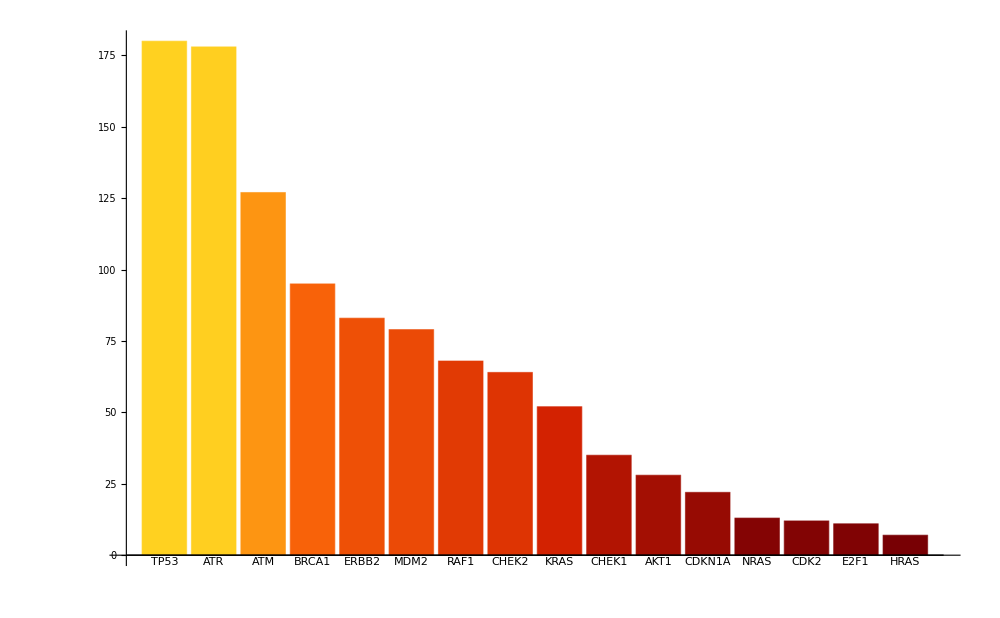

```mathematica
(* Search the main genes mutations data *)
getMutations = Function[gene,
{gene, GeneLookup[dataset, gene, "MUTATIONS_COUNT"]}
];
mainGenesHist = getMutations/@ Keys[geneIDs16]
mainGenesHist = Reverse[Sort[Apply[Labeled,Reverse[mainGenesHist,2],{1}]]]

bars = BarChart[mainGenesHist, ImageSize->1000, ColorFunction->ColorData["SolarColors"], BaseStyle->{FontFamily-> "ArialBlack"}]
```

```mathematica
If[export,
Export["./bars.svg", bars]
];
```

{180TP53,178ATR,127ATM,95BRCA1,83ERBB2,79MDM2,68RAF1,64CHEK2,52KRAS,35CHEK1,28AKT1,22CDKN1A,13NRAS,12CDK2,11E2F1,7HRAS}

{180,178,127,95,83,79,68,64,52,35,28,22,13,12,11,7}

Dataset[<>]

{Piecewise[{{1/16, 7≤x≤22}, {0, True}}],Piecewise[{{(5.04348×10^-7 14.5^x)/(x!), x≥0}, {0, True}}],Piecewise[{{0.0000240439 0.446154^x Binomial[17+x,17], x≥0}, {0, True}}],Piecewise[{{0.000203142 0.655172^(-5+x) (-4+x) (-3+x) (-2+x) (-1+x), x≥5}, {0, True}}],Piecewise[{{0.439394^x 0.560606^(33-x) Binomial[33,x], 0≤x≤33}, {0, True}}]}

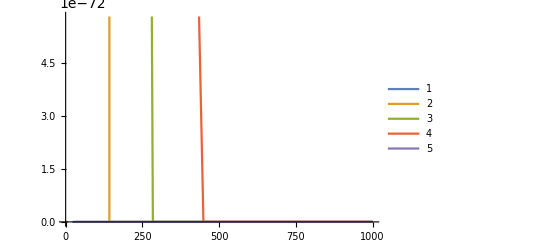

```mathematica
mainGenesHist
mainGenesRaw = Reverse[Sort[(#[[2]])& /@(getMutations /@ Keys[geneIDs16])]]
mainGenesFits = FindDistribution[mainGenesRaw, 5, All, PerformanceGoal->"Quality", TargetFunctions->"Discrete"]
PDFs = (PDF[#,x]&) /@ Normal[Keys[mainGenesFits]]
Plot[PDFs,{x,0,1000}, 
PlotLegends -> Automatic
]
```

```mathematica
If[export,
Export["./bars.png",bars]
]
```

./bars.png

```mathematica
(* Function to select the labeled data for a gene *)
getLabeledPlotData = Function[gene,
Labeled[(GeneLookup[dataset, gene, #]&)/@ {"MUTATIONS_COUNT", "GENE_COUNT"}, gene]
];
getLegendedPlotData = Function[gene,
Legended[(GeneLookup[dataset, gene, #]&)/@ {"MUTATIONS_COUNT", "GENE_COUNT"}, gene]
];
```

```mathematica
mainGenesDataLabeled = getLabeledPlotData/@ Keys[geneIDs16] 
mainGenesDataLegended = getLegendedPlotData/@ Keys[geneIDs16]
```

{{12,1262}CDK2,{180,19}TP53,{79,74}MDM2,{95,67}BRCA1,{83,81}ERBB2,{127,50}ATM,{28,442}AKT1,{35,261}CHEK1,{64,110}CHEK2,{11,1197}E2F1,{178,19}ATR,{7,893}HRAS,{52,144}KRAS,{13,1219}NRAS,{22,738}CDKN1A,{68,82}RAF1}

{{12,1262},{180,19},{79,74},{95,67},{83,81},{127,50},{28,442},{35,261},{64,110},{11,1197},{178,19},{7,893},{52,144},{13,1219},{22,738},{68,82}}

```mathematica
rawMainGenesData = Graphics[Text[mainGenesDataLabeled], ImageSize->{1000,{50}}]
```

-Graphics-

```mathematica
If[export,
Export["./raw_main_genes_data.png",rawMainGenesData]
]
```

./raw_main_genes_data.png

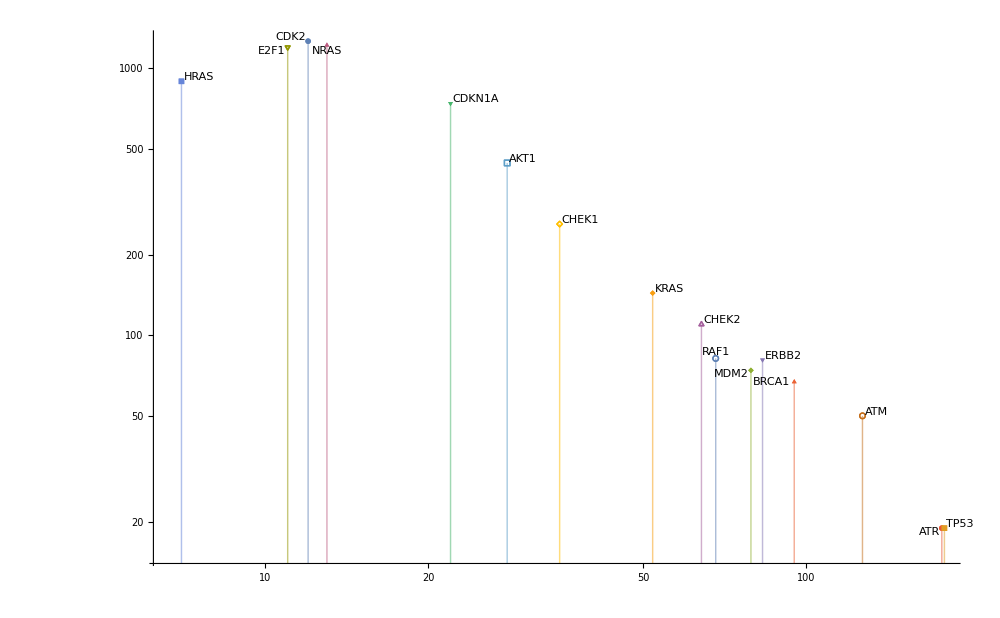

```mathematica
mainGenesSimple = ListLogLogPlot[
Map[({#})&,mainGenesDataLabeled], 
PlotMarkers->{Automatic,Large}, Filling->Axis, ImageSize->1000
]
```

```mathematica
If[export,
Export["./mainGenesSimple.png", mainGenesSimple]
]
```

./mainGenesSimple.png

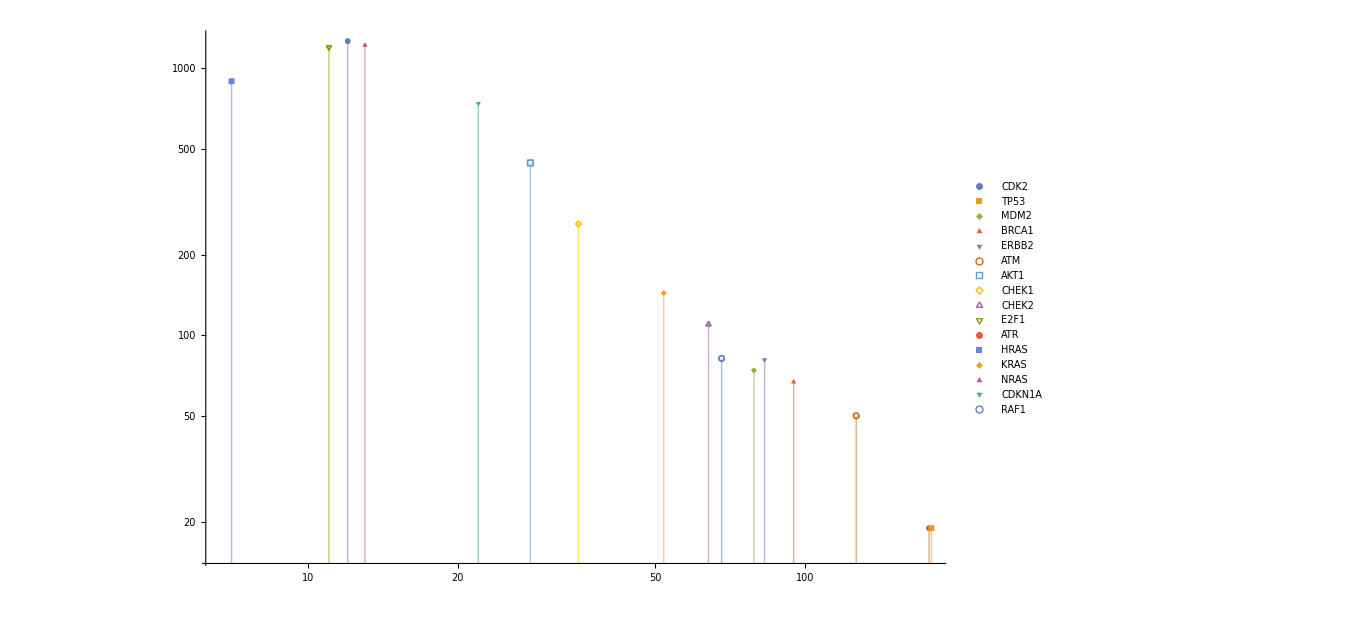

```mathematica
ListLogLogPlot[Map[({#})&,mainGenesDataLegended], PlotMarkers->{Automatic,Large}, Filling->Axis, ImageSize->1000]
```

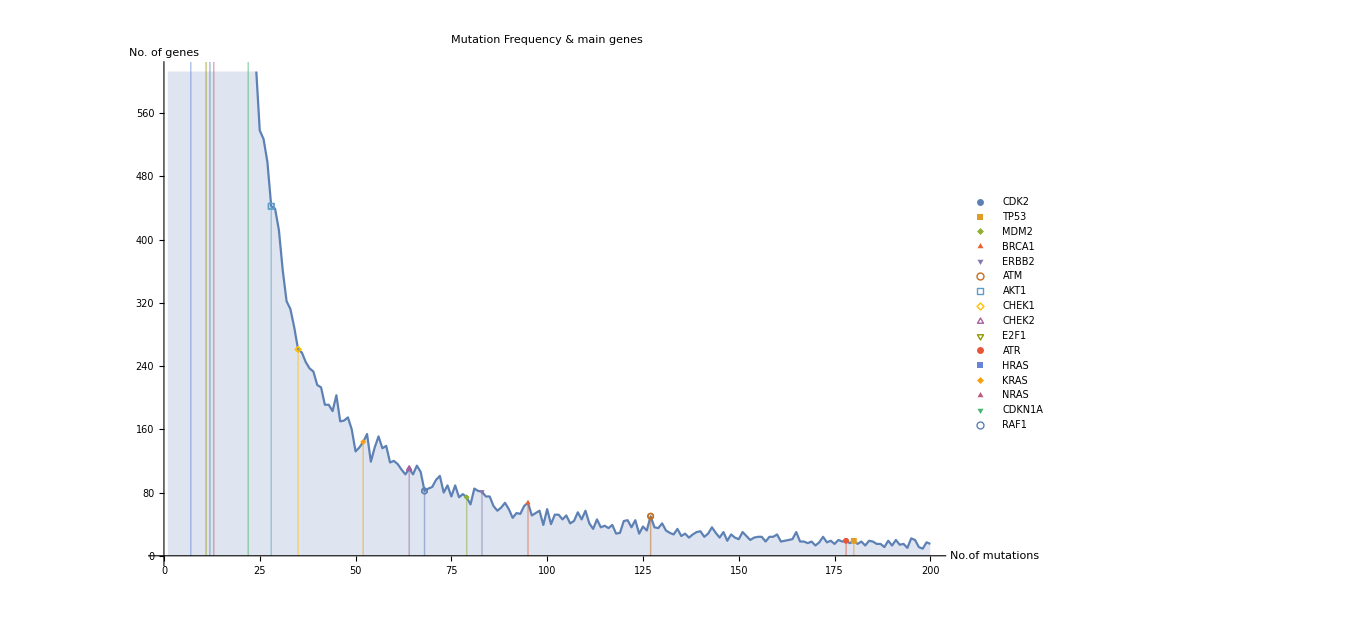

```mathematica
mainGenesPlot = Show[
ListPlot[distribution[[;;200]], 
Filling->Bottom,ImageSize->1000, PlotLabel->"Mutation Frequency & main genes", AxesLabel->{"No.of mutations","No. of genes"}, Joined->True,BaseStyle->{FontFamily-> "ArialBlack"}
],
ListPlot[Map[({#})&,mainGenesDataLegended], PlotMarkers->{Automatic,Large}, Filling->Axis,PlotRange->All, ImageSize->1000, BaseStyle->{FontFamily-> "ArialBlack"}, PlotLegends->Automatic]
, BaseStyle->{FontFamily-> "ArialBlack"}
]
```

```mathematica
If[export,
Export["./mainGenesPlot.svg", mainGenesPlot]
]
```

./mainGenesPlot.svg

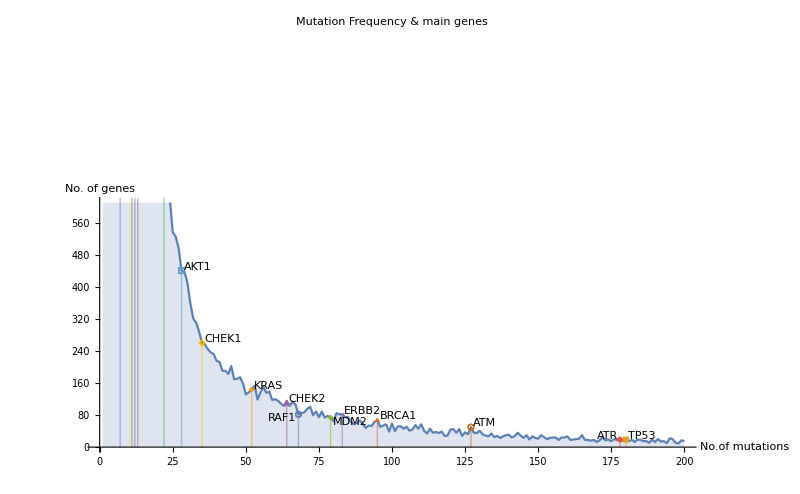

```mathematica
mainGenesZoomPlot = Show[
ListPlot[distribution[[;;200]], 
Filling->Bottom,ImageSize->800, PlotLabel->"Mutation Frequency & main genes", AxesLabel->{"No.of mutations","No. of genes"}, Joined->True
],
ListPlot[Map[({#})&,mainGenesDataLabeled], PlotMarkers->{Automatic,Large}, Filling->Axis,PlotRange->All, ImageSize->800, LabelStyle->{FontFamily-> "ArialBlack"}]
]
```

```mathematica
If[export,
Export["./mainGenesZoomPlot.svg", mainGenesZoomPlot]
]
```

./mainGenesZoomPlot.svg

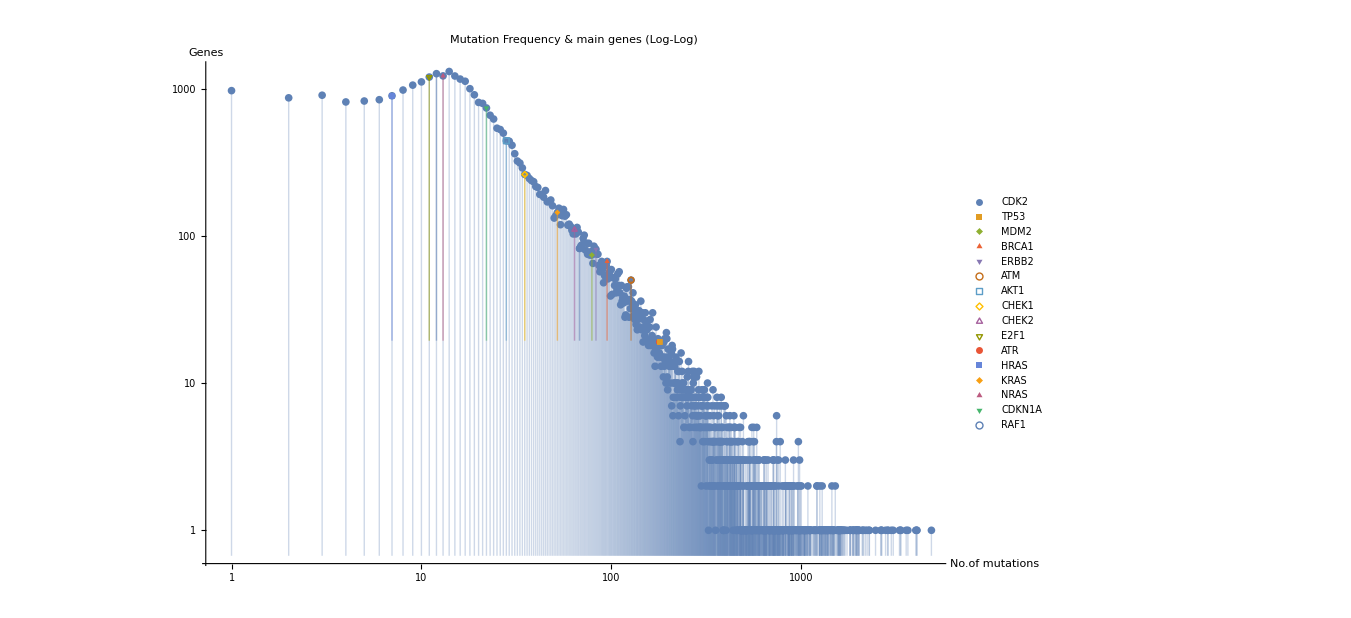

```mathematica
mainGenesLogLogPlot=Show[
ListLogLogPlot[distribution, 
Filling->Bottom,ImageSize->1000, PlotLabel->"Mutation Frequency & main genes (Log-Log)", AxesLabel->{"No.of mutations","Genes"}
],
ListLogLogPlot[Map[({#})&,mainGenesDataLegended], PlotMarkers->{Automatic,Large}, Filling->Axis,PlotRange->{-10000, 1100}, ImageSize->1000]
]
```

```mathematica
If[export,
Export["./mainGenesLogLogPlot.png", mainGenesLogLogPlot]
]
```

./mainGenesLogLogPlot.png

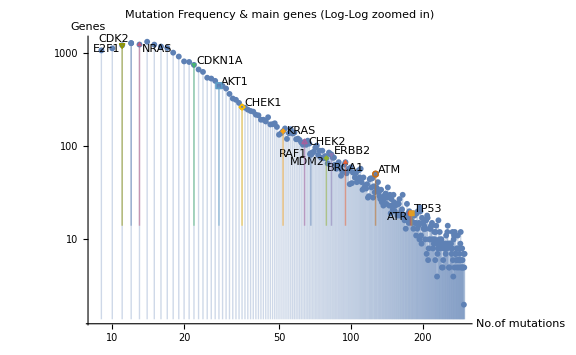

```mathematica
mainGenesLogLogZoomPlot=Show[
ListLogLogPlot[distribution[[9;;300]], 
Filling->Bottom,ImageSize->Large, PlotLabel->"Mutation Frequency & main genes (Log-Log zoomed in)", AxesLabel->{"No.of mutations","Genes"}
],
ListLogLogPlot[Map[({#})&,mainGenesDataLabeled], PlotMarkers->{Automatic,Large}, Filling->Axis,PlotRange->All,ImageSize->Large]
]
```

```mathematica
If[export,
Export["./mainGenesLogLogZoomPlot.png", mainGenesLogLogZoomPlot]
]
```

./mainGenesLogLogZoomPlot.png

```mathematica
mainGenesPlots=GraphicsGrid[
{
{
mainGenesPlot,
mainGenesZoomPlot
}
,
{
mainGenesLogLogPlot,
mainGenesLogLogZoomPlot
}
}
,
ImageSize->1800
]
```

-Graphics-

```mathematica
If[export,
Export["./mainGenesPlots.png", mainGenesPlots]
]
```

./mainGenesPlots.png

## Data normalization

```mathematica
a = {{1,2},{2,3}, {3,4},{4,5},{7,5}}
```

{{1,2},{2,3},{3,4},{4,5},{7,5}}

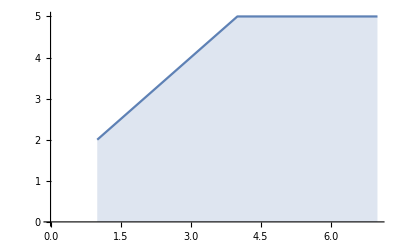

```mathematica
ListPlot[a, Filling->Bottom, Joined->True]
```

```mathematica
DiscreteIntegral =Total[ #[[All, 2]] ]&
```

Total[#1⟦All,2⟧]&

```mathematica
DiscreteIntegral[a]
```

19

```mathematica
DiscreteIntegral[distribution]
```

39985

```mathematica
NormalizePlot[plot_] := Module[{sum = DiscreteIntegral[plot]},
({#[[1]],#[[2]]/sum} &) /@plot
]
```

```mathematica
normalizedData = NormalizePlot[distribution]; DiscreteIntegral[normalizedData]
```

1

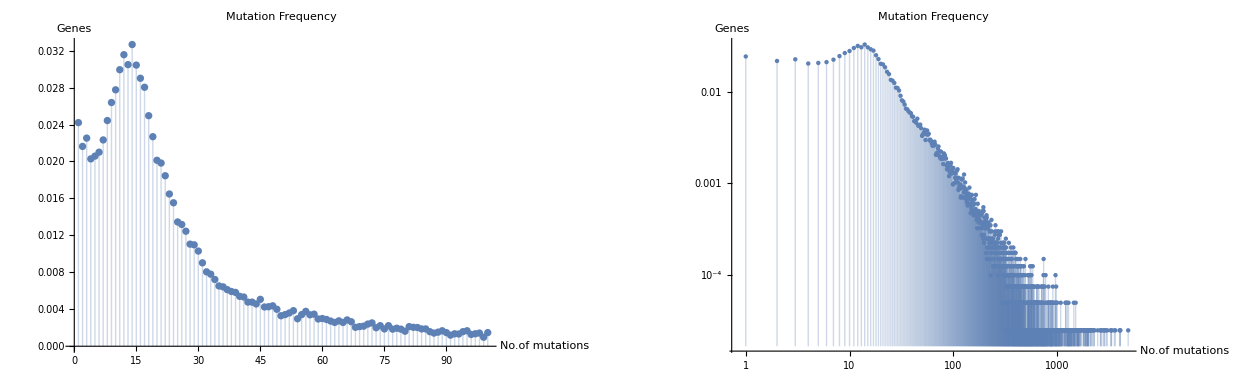

```mathematica
GraphicsGrid[
{{
ListPlot[normalizedData[[;;100]], 
Filling->Bottom,ImageSize->Large, PlotLabel->"Mutation Frequency", AxesLabel->{"No.of mutations","Genes"}
], 
ListLogLogPlot[normalizedData, 
Filling->Bottom, Joined -> False,ImageSize->Large, PlotLabel->"Mutation Frequency", AxesLabel->{"No.of mutations","Genes"}
]
}}
]
```

## Poisson Fit

```mathematica
GetLambda = Total[(#[[1]]*#[[2]]&) /@ #1] / Total[ (#[[ 2]]&) /@ #1]&
```

Total[(#1⟦1⟧ #1⟦2⟧&)/@#1]/Total[(#1⟦2⟧&)/@#1]&

```mathematica
GetMean = GetLambda;
```

```mathematica
λ=GetLambda[normalizedData[[1;;150]]]
```

536694/18425

```mathematica
N[λ]
```

29.1286

```mathematica
Poisson = PDF[PoissonDistribution[#1], #2]&
```

PDF[PoissonDistribution[#1],#2]&

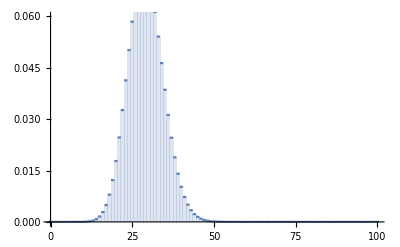

```mathematica
poissonPlot =DiscretePlot[Poisson[λ,k], {k, 0, 100}, ExtentSize->Full,PlotRange->{0,0.06}]
```

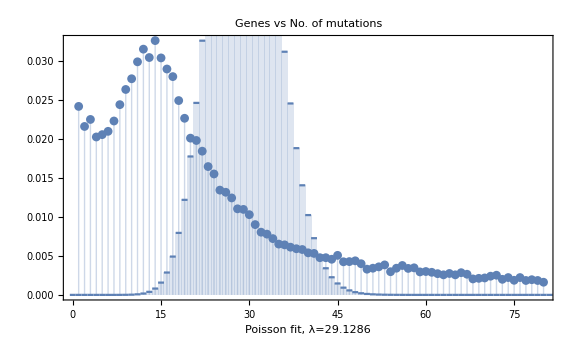

```mathematica
poissonFitPlot = Show[
ListPlot[normalizedData[[;;80]], 
Filling->Bottom,ImageSize->Large, PlotLabel->"Mutation Frequency", AxesLabel->{"No.of mutations","Genes"}
],
poissonPlot,
Frame->True,
ImageSize->Large,
PlotLabel -> "Genes vs No. of mutations",
FrameLabel->{{None,None},{RawBoxes[RowBox[{RowBox[{"Poisson"," ","fit"}],","," ",RowBox[{"λ","=",ToString[N[λ]]}]}]],None}},PlotLabel->"Genes vs No. of mutations",LabelStyle->{GrayLevel[0]}
]
```

```mathematica
If[export,
Export["./poissonFitPlot.png", poissonFitPlot]
]
```

./poissonFitPlot.png

## Log-Normal fit

This has not much sense since the Log-Normal distribution is a continuous distribution, but has been left here for completeness.

```mathematica
MapToPlotY[f_, p_] := ( {#[[1]],f[#[[2]]]}&  ) /@ p
```

```mathematica
MapToPlotX[f_, p_] := ( {f[#[[1]]],#[[2]]}&  ) /@ p
```

```mathematica
a
MapToPlotY[Log, a]
```

{{1,2},{2,3},{3,4},{4,5},{7,5}}

{{1,Log[2]},{2,Log[3]},{3,Log[4]},{4,Log[5]},{7,Log[5]}}

```mathematica
a
MapToPlotX[Log, a]
```

{{1,2},{2,3},{3,4},{4,5},{7,5}}

{{0,2},{Log[2],3},{Log[3],4},{Log[4],5},{Log[7],5}}

1.

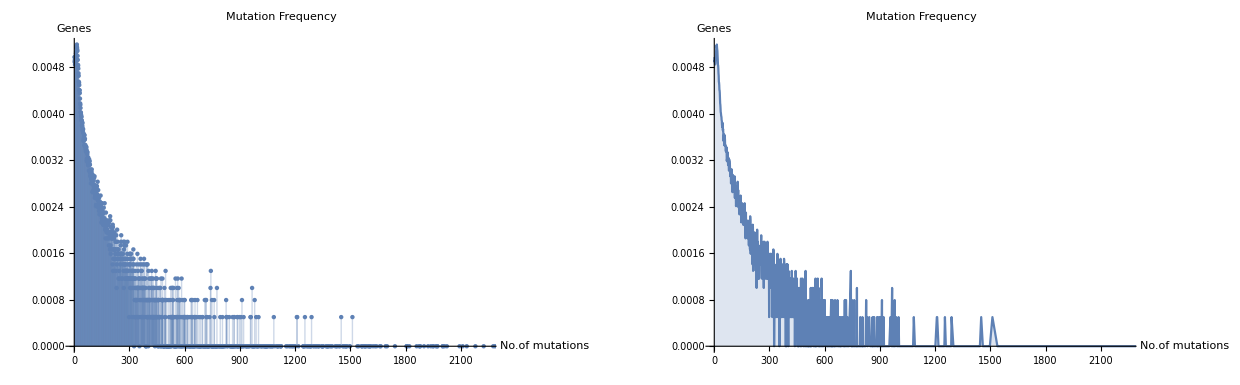

```mathematica
logYData = MapToPlotY[Log, distribution];
normLogYData = NormalizePlot[logYData];
DiscreteIntegral[normLogYData] // N
GraphicsGrid[
{{
ListPlot[#, 
Filling->Bottom,ImageSize->Large, PlotLabel->"Mutation Frequency", AxesLabel->{"No.of mutations","Genes"}
], 
ListPlot[#, 
Filling->Bottom, Joined -> True,ImageSize->Large, PlotLabel->"Mutation Frequency", AxesLabel->{"No.of mutations","Genes"}
]
}}
]& @ normLogYData
```

```mathematica
logXData = MapToPlotX[Log, distribution];
```

```mathematica
normLogXData = NormalizePlot[logXData];
DiscreteIntegral[normLogXData]
```

1

```mathematica
logXPlot = ListPlot[ normLogXData, 
Joined-> True,
Filling->Bottom, 
ImageSize->Large, 
PlotLabel->"Mutation Frequency", 
AxesLabel->{"No.of mutations","Genes"}
];
```

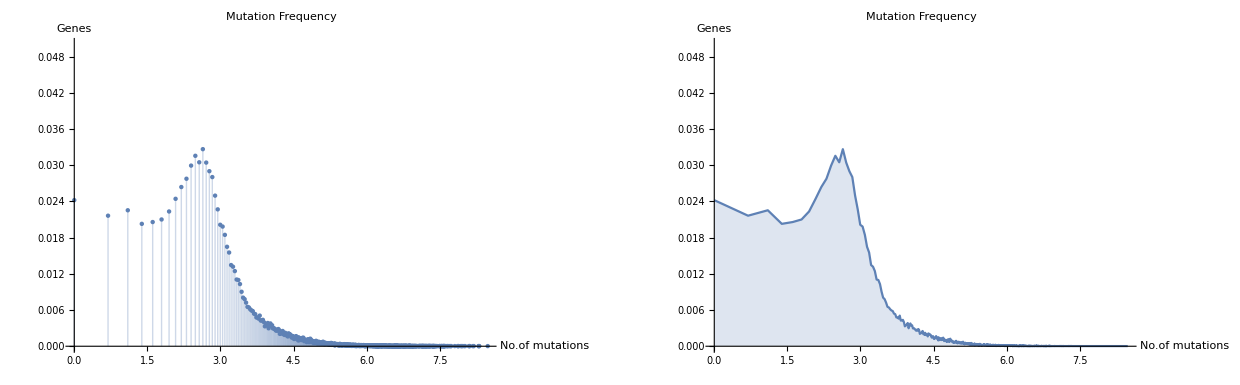

```mathematica
GraphicsGrid[
{{
ListPlot[#, 
Filling->Bottom,ImageSize->Large, PlotLabel->"Mutation Frequency", AxesLabel->{"No.of mutations","Genes"}, PlotRange->{0,0.05}
], 
ListPlot[#, 
Filling->Bottom, Joined -> True,ImageSize->Large, PlotLabel->"Mutation Frequency", AxesLabel->{"No.of mutations","Genes"}, PlotRange->{0,0.05}
]
}}
]& @ normLogXData
```

```mathematica
μ = GetMean[normLogXData[[5;;150]]];N[μ]
```

3.1173

```mathematica
ExpandFreqPair = Module[{i, l={}},
For[i=#[[2]],i>0, i--,
l= Append[l,#[[1]]];
];
l
]&;
(* Test *)
ExpandFreqPair[{2,3}]
```

{2,2,2}

```mathematica
ExpandFreqTable = Module[{l={}}, 
For[i=1, i≤Length[#],i++,
l = l // Append[ExpandFreqPair[#[[i]]]]
];
l // Flatten
]&;
ExpandFreqTable[{{1,2},{2,4}}]
```

{1,1,2,2,2,2}

```mathematica
σ = Variance[ExpandFreqTable[normLogXData]]^1/2; N[σ]
```

0.637897

```mathematica
Gauss = PDF[NormalDistribution[#1,#2],#3]&
```

PDF[NormalDistribution[#1,#2],#3]&

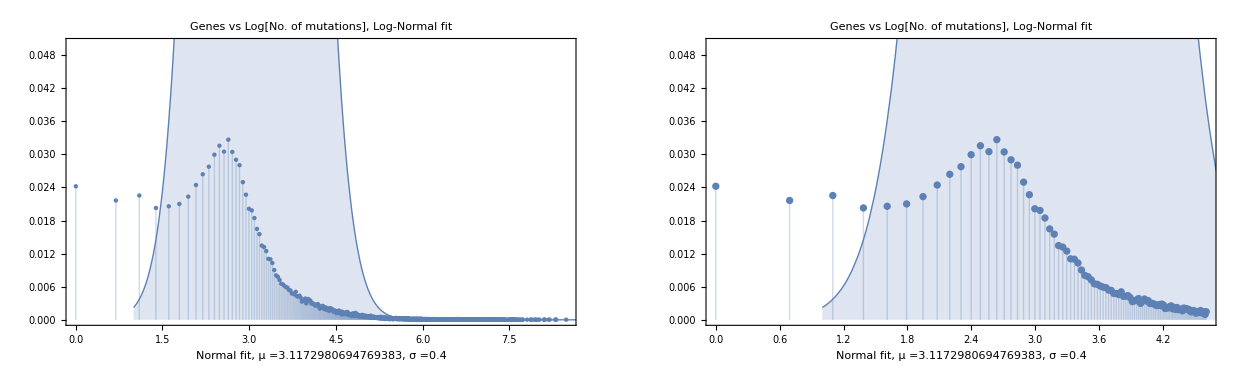

```mathematica
logNormalFitPlot=GraphicsGrid[
{{
(* Plots all data *)
Show[
ListPlot[ normLogXData, 
Filling->Bottom, ImageSize->Large, PlotLabel->"Mutation Frequency", AxesLabel->{"No.of mutations","Genes"},PlotRange->{0,0.05}
],
Plot[Gauss[μ,0.63,x],{x,1,9},PlotStyle->Thick, Filling->Bottom],
Frame->True,
ImageSize->Large,
FrameLabel->{{None,None},{RawBoxes[RowBox[{RowBox[{"Normal fit"}],", ",RowBox[{"μ =",N[μ]}],", ",RowBox[{"σ =",0.4}]}]],None}},PlotLabel->"Genes vs Log[No. of mutations], Log-Normal fit",LabelStyle->{GrayLevel[0]}
], 
(* Plots zoomed data *)
Show[
ListPlot[ normLogXData[[;;100]], 
Filling->Bottom, ImageSize->Large,PlotLabel->"Mutation Frequency", AxesLabel->{"No.of mutations","Genes"}, PlotRange->{0,0.05}
],
Plot[Gauss[μ,0.63,x],{x,1,9},PlotStyle->Thick, Filling->Bottom],
Frame->True,
ImageSize->Large,
FrameLabel->{{None,None},{RawBoxes[RowBox[{RowBox[{"Normal fit"}],", ",RowBox[{"μ =",N[μ]}],", ",RowBox[{"σ =",0.4}]}]],None}},PlotLabel->"Genes vs Log[No. of mutations], Log-Normal fit",LabelStyle->{GrayLevel[0]}
]
}}
]
```

```mathematica
If[export,
Export["./logNormalFitPlot.png", logNormalFitPlot]
]
```

./logNormalFitPlot.png

## Finding best distribution for raw data

```mathematica
p = {5,3}
```

{5,3}

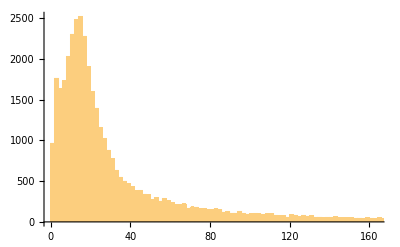

```mathematica
histogram = Show@Histogram[rawSamples,3000, ImageSize->Full]
```

```mathematica
If[export,
Export["./histogram.png", histogram]
]
```

./histogram.png

```mathematica
BestDistribution = (PDF[FindDistribution[#, PerformanceGoal->"Quality"], x])&;
```

```mathematica
bestFits = FindDistribution[rawSamples, 5, All, PerformanceGoal->"Quality"]
```

Dataset[<>]

```mathematica
distributions = Normal[Keys[bestFits]]
```

{MixtureDistribution[{0.75899,0.24101},{NegativeBinomialDistribution[2,0.0990607],GeometricDistribution[0.00372693]}],MixtureDistribution[{0.708216,0.291784},{NegativeBinomialDistribution[2,0.0889254],LogSeriesDistribution[0.99938]}],MixtureDistribution[{0.776215,0.223785},{GeometricDistribution[0.0477655],GeometricDistribution[0.0035532]}],LogSeriesDistribution[0.997009],GeometricDistribution[0.0126212]}

```mathematica
GetPDF= PDF[#,x]&
```

PDF[#1,x]&

```mathematica
PDFs=GetPDF /@distributions
```

{Piecewise[{{0., x<0}, {0.000898226 0.996273^x+0.00744798 0.900939^x (1+x), True}}],Piecewise[{{0., x<0}, {0.+0.00560038 0.911075^x (1+x), 0≤x<1}, {(0.0395023 0.99938^x)/x+0.00560038 0.911075^x (1+x), True}}],Piecewise[{{0., x<0}, {0.0370763 0.952235^x+0.000795155 0.996447^x, True}}],Piecewise[{{(0.172053 0.997009^x)/x, x≥1}, {0, True}}],Piecewise[{{0.0126212 0.987379^x, x≥0}, {0, True}}]}

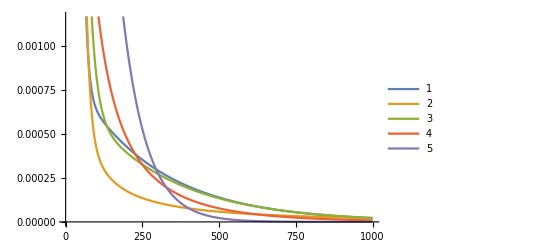

```mathematica
Plot[PDFs,{x,0,1000}, 
PlotLegends -> Automatic
]
```

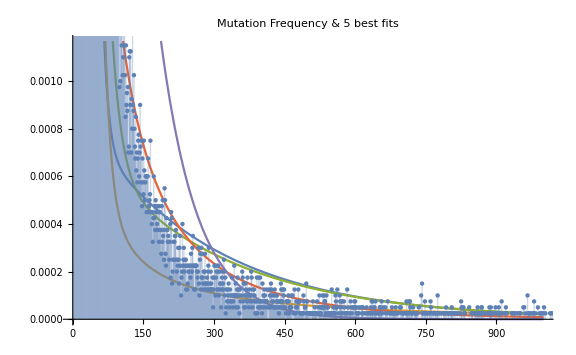

```mathematica
fits = GraphicsGrid[{{
Show[
Plot[PDFs,{x,0,1000}, 
ImageSize->Large
],
ListPlot[normalizedData, 
Filling->Bottom,ImageSize->Large,  AxesLabel->{"No.of mutations","Genes"}, PlotRange->{0,0.05}
],
PlotLabel-> "Mutation Frequency & 5 best fits"
]},
{Show[
Plot[PDFs,{x,0,100}, 
PlotLegends -> Automatic,
ImageSize->Large
],
ListPlot[normalizedData[[;;100]], 
Filling->Bottom,ImageSize->Large, AxesLabel->{"No.of mutations","Genes"}, PlotRange->{0,0.05}
],
PlotLabel-> "Mutation Frequency & 5 best fits (Zoomed in)"
]
},
{Show[
LogLogPlot[PDFs,{x,1,300}, 
PlotLegends -> Automatic,
ImageSize->Large
],
ListLogLogPlot[normalizedData, 
Filling->Bottom,ImageSize->Large, PlotLabel->"Mutation Frequency", AxesLabel->{"No.of mutations","Genes"}
],
PlotLabel-> "Mutation Frequency & 5 best fits (Log-Log)"
]}}]
```

```mathematica
If[export,
Export["./fits.png", fits]
]
```

./fits.png

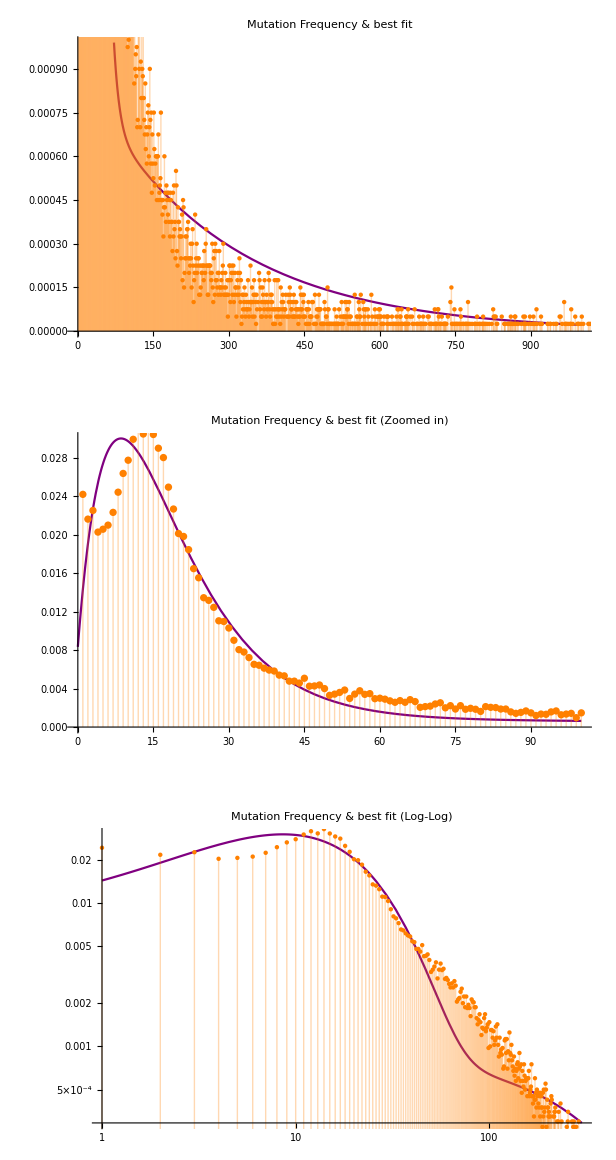

```mathematica
bestFitPlot= GraphicsGrid[{{
Show[
Plot[PDFs[[1]],{x,0,1000}, 
ImageSize->Large,PlotStyle->Purple
],
ListPlot[normalizedData, 
Filling->Bottom,ImageSize->Large, PlotLabel->"Mutation Frequency", AxesLabel->{"No.of mutations","Genes"},PlotStyle->Orange, PlotRange->{0,0.05}
],
PlotLabel-> "Mutation Frequency & best fit"
]},
{Show[
Plot[PDFs[[1]],{x,0,100}, 
PlotLegends -> Automatic,ImageSize->Large,PlotStyle->Purple
],
ListPlot[normalizedData[[;;100]], 
Filling->Bottom,ImageSize->Large, PlotLabel->"Mutation Frequency", AxesLabel->{"No.of mutations","Genes"},PlotStyle->Orange, PlotRange->{0,0.05}
],
PlotLabel-> "Mutation Frequency & best fit (Zoomed in)"
]
},
{Show[
LogLogPlot[PDFs[[1]],{x,1,300}, 
PlotLegends -> Automatic,ImageSize->Large,PlotStyle->Purple
],
ListLogLogPlot[normalizedData, 
Filling->Axis,ImageSize->Large, PlotLabel->"Mutation Frequency", AxesLabel->{"No.of mutations","Genes"},PlotStyle->Orange
],
PlotLabel-> "Mutation Frequency & best fit (Log-Log)"
]}}]
```

```mathematica
If[export,
Export["./genes_mutations_bestFitPlot.png", bestFitPlot]
]
```

./genes_mutations_bestFitPlot.png

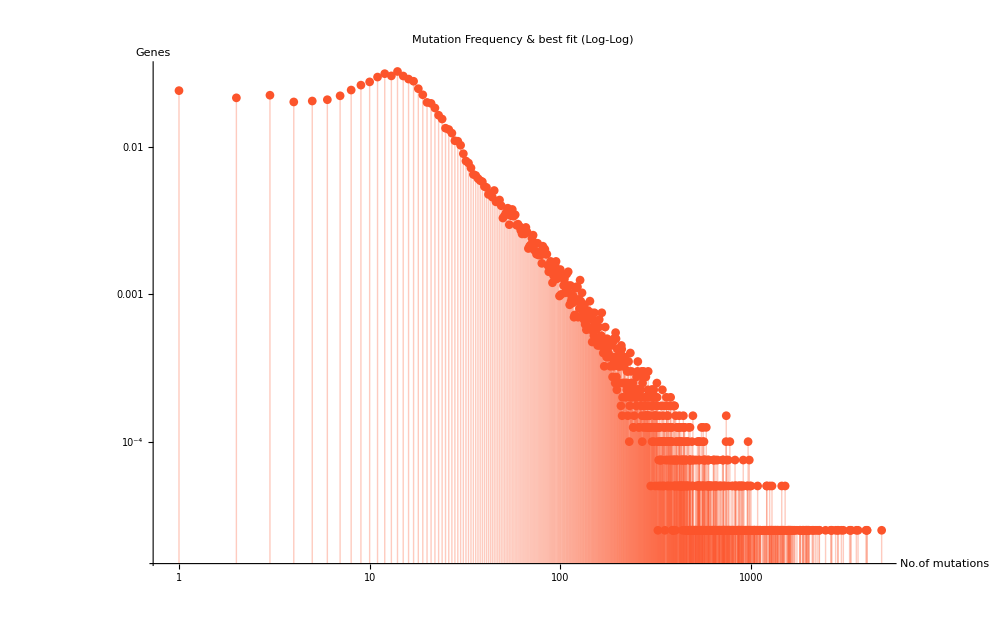

```mathematica
bestFitSimplePlot = Show[
ListLogLogPlot[normalizedData, 
Filling->Axis,ImageSize->1000, PlotLabel->"Mutation Frequency", AxesLabel->{"No.of mutations","Genes"}, Joined->False, PlotMarkers->Automatic, PlotStyle->RGBColor[0.99,0.33,0.17]
],
PlotLabel-> "Mutation Frequency & best fit (Log-Log)"
]
```

```mathematica
If[export,
Export["./genes_mutations_bestFitSimplePlot.png", bestFitSimplePlot]
]
```

./genes_mutations_bestFitSimplePlot.png

```mathematica
f = FindFormula[normalizedData]
```

Piecewise[{{0.0298727-0.000758903 #1+7.08134×10^-6 #1^2-3.02075×10^-8 #1^3+5.96844×10^-11 #1^4-4.4283×10^-14 #1^5, 1.≤#1<467.}, {0, True}}]&

```mathematica
f[x]
```

Piecewise[{{0.0298727-0.000758903 x+7.08134×10^-6 x^2-3.02075×10^-8 x^3+5.96844×10^-11 x^4-4.4283×10^-14 x^5, 1.≤x<467.}, {0, True}}]

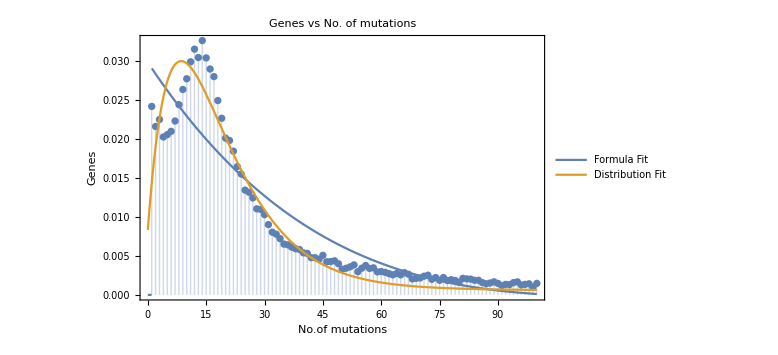

```mathematica
formulaFitPlot=Show[
ListPlot[ normalizedData[[;;100]], 
Filling->Bottom, 
ImageSize->Large, 
PlotLabel->"Mutation Frequency", 
AxesLabel->{"No.of mutations","Genes"},
Joined->False
],
Plot[{f[x],PDFs[[1]]},{x,0,100}, 
PlotRange-> {0, 0.050},
PlotLegends->{"Formula Fit", "Distribution Fit"}
],
Frame->True,
ImageSize->Large,
PlotLabel->"Genes vs No. of mutations",LabelStyle->{GrayLevel[0]},
AxesLabel->{"No.of mutations","Genes"}
]
```

```mathematica
If[export,
Export["./genes_mutations_formulaFitPlot.png", formulaFitPlot]
]
```

./genes_mutations_formulaFitPlot.png